## Euler’s method of solving dy/dx = f(x,y), y(x_0)=y_0

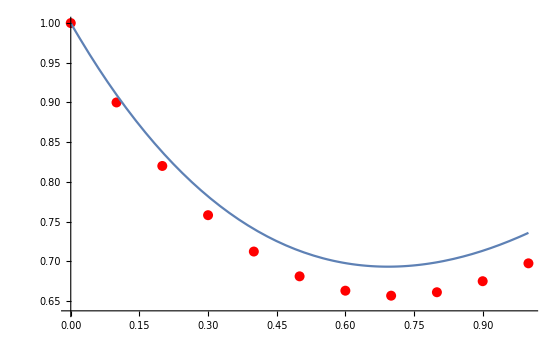

```mathematica
f[x_,y_]:=x-y;
x=0; y=1;                   (* initial values x0, y0 *)

sol={{x,y}};    
h=.1;
xf=1.;

While[x<xf,
y=y+h f[x,y];      (* Euler's method = Taylor series of order 1 method *)
x=x+h;
AppendTo[sol,{x,y}]];

g1=ListPlot[sol,PlotStyle->Red];
g2=Plot[x-1+2E^(-x),{x,0,xf}];    (* exact solution *)
Show[g1,g2]
```

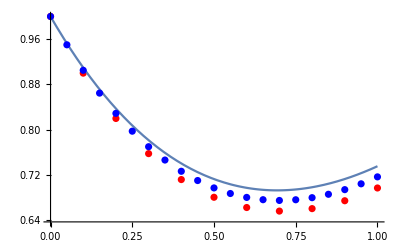

```mathematica
x=0; y=1;                   (* initial values x0, y0 *)

sol={{x,y}};    
h=.05;
xf=1.;

While[x<xf,
y=y+h f[x,y];      (* Euler's method = Taylor series of order 1 method *)
x=x+h;
AppendTo[sol,{x,y}]];

g3=ListPlot[sol,PlotStyle->Blue];
Show[g1,g2,g3]
```

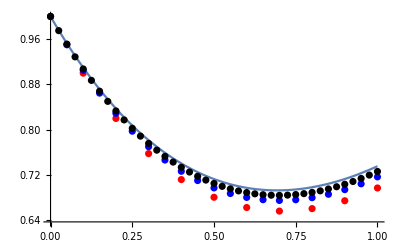

```mathematica
x=0; y=1;                   (* initial values x0, y0 *)

sol={{x,y}};    
h=.025;
xf=1.;

While[x<xf,
y=y+h f[x,y];      (* Euler's method = Taylor series of order 1 method *)
x=x+h;
AppendTo[sol,{x,y}]];

g4=ListPlot[sol,PlotStyle->Black];
Show[g1,g2,g3,g4]
```